```mathematica
BeginPackage["typ`"];
Clear["typ`*"]
typmath;
mmatotyp;
mmatotyp2;
typcell;
typstep;
eqalign;
typsplus;
typQsy;
Begin["`Private`"];
Clear["typ`Private`*"]
Attributes[typstep]={HoldAllComplete};
typstep[in_]:=typcell["",""]["$"<>mmatotyp2[][HoldComplete[in]]<>"=$
"<>"$"<>mmatotyp2[][in]<>"$"];
(*sypfun={typToString,typQsy,typTimes,typDerivative,typDerivative,SR,typPower};*)
Attributes[typHold]={HoldAll};
typToString[in3___,typToString[in___],in2___]:=typToString[in3,in,in2];
typToString[in_String]:=in;
typSR[typList[in___String],sr___String]:=StringRiffle[{in},sr];
typSR[typList[in___Symbol],sr___String]:=StringRiffle[{in},sr];
typQsy[in_]:=in;
typQsy[in_Symbol]:=ToString[in];
typQfun[in_]:=in;
typQfun[in_Symbol[___]]:=ToString[in];
typTimes[o1___,HoldPattern[p:typPlus[__]],o2___]:=typTimes[o1,typbk[p],o2];
typDerivative[ee___][f_Symbol][x___]:=typsplus["diff_(",
typSR[typList@@Flatten[MapThread[Table[typQfun[typQsy[#2]],#1]&,{{ee},{x}}]]," "],")",f[x]];
typPower[p:typsplus["diff_(",___],o_]:=typPower[typbk[p],o];
typPower[typSuperStar[p_],p2_]:=typPower[typbk[typSuperStar[p]],p2];
typTimes[o1___,HoldPattern[p:typPlus[__]],o2___]:=typTimes[o1,typbk[p],o2];
typTimes[o1___,o2_NumberQ]:=typTimes[o2,o1];
(*typTimes[o1___,o3:f_[___]?(Not[NumberQ[#]]&),o4___,o2_Symbol]:=(typTimes[o2,o1,o3,o4]);*)
typTimes[o1___,o2_typTimes,o3___]:=typTimes[o1,Sequence@@o2,o3];
(*typPower[HoldPattern[p:typPlus[__]],o2___]:=typPower[typbk[p],o2];*)
typeqalign[p:{__String}]:=(typColumn[StringReplace[#,"="->"&="]&/@p]);

typIdentity[in_,___]:=in
(*
typunfun[funname_String][var___String]:=typsplus[funname,"(",typsplus@@Riffle[{var},","],")"];*)
typunfun[funname_String][var___]:=typsplus["\"",funname,"\"","(",typsplus@@Riffle[typQsy /@{var},","],")"];
(*typQsysfun[in_]:=And[UpperCaseQ@StringTake[SymbolName[in],1],in=!=HoldComplete];*)
typQsysfun[in_]:=And[Context[in]==="System`",in=!=HoldComplete];
typQtypfun[in_]:=Or[StringContainsQ[SymbolName[in],"typ"],in===HoldComplete];
typstrlist[in___]:=typsplus["{",typsplus@@Riffle[typQsy/@{in},","],"}"];
typIntegrate[exp_,sy_Symbol]:=typsplus["integral ",typQsy@exp," dd(",typToString[sy],")"];
typIntegrate[exp_,{sy_Symbol,down_,up_}]:=typsplus["integral_(",typQsy@down,")^(",typQsy@up,") ",typQsy@exp," dd(",typToString[sy],")"]
typD[exp_,var__]:=typsplus["partial_(",typsplus@@Riffle[typQsy/@{var}," "],") ",exp];
typD[exp_,p:{_,_}..]:=typsplus["partial_(",typsplus@@Riffle[Flatten[Table[typQsy[#[[1]]],#[[2]]]&/@{p}]," "],") ",exp];
typSuperStar[p_String]:=typsplus[p,"^*"];
typSuperStar[p_Symbol]:=typsplus[typToString[p],"^*"];
typPlus[p_]:=p;
typPlus[p1___,p2_Symbol,p3___]:=typPlus[p1,typToString[p2],p3];
typPlus[p___String]:=StringRiffle[{p},"+"];
typPlus/:typTimes[p1___,HoldPattern[typPlus[p2___]],p3___]:=typTimes[p1,typbk[typPlus[p2]],p3];
typPlus/:typConjugate[HoldPattern[typPlus[p___]]]:=(typConjugate[typbk[typPlus[p]]]);
typPlus/:typPower[HoldPattern[typPlus[p__]],o2___]:=typPower[typbk[typPlus[p]],o2];

typTimes[p1___,"-1",p2_Symbol,p3___]:=(typTimes[p1,typsplus["-",typToString[p2]],p3]);
typTimes[p1___,"1",p2_Symbol,p3___]:=typTimes[p1,typToString[p2],p3];
typTimes[p1___,p2_Symbol,p3___]:=typTimes[p1,typToString[p2],p3];
typTimes["1",p___String]:=StringRiffle[{p}," "];
typTimes["-1",p___String]:=StringRiffle[{"-",p}," "];
typTimes[p___String]:=StringRiffle[{p}," "];
typTimes[p_]:=p;
typPower[E,p_String]:=StringJoin["e^(",p,")"];
typPower[E,p_Symbol]:=StringJoin["e^(",ToString@p,")"];
typPower[p2_String,p_String]:=StringJoin[p2,"^(",p,")"];
typPower[p2_Symbol,p_String]:=typsplus[typToString[p2],"^(",p,")"];
typExp[in_]:=typPower[E,typQsy@in];
typRational[p1_,p2_]:=(Echo@typsplus["frac(",typToString@p1,",",typToString@p2,")"]);
typbk[p_String]:=StringJoin["(",p,")"];
typsplus[p___String]:=StringJoin[{p}];
typEqual[p1_Symbol,p2_Symbol]:=typsplus[ToString[p1],"=",ToString@p2];
typEqual[p1_Symbol,p2_String]:=typsplus[typToString[p1],"=",p2];
typEqual[p1_String,p2_Symbol]:=typsplus[p1,"=",typToString@p2];
typEqual[p1_String,p2_String]:=typsplus[p1,"=",p2];
typRule[a_String,b_String]:=typsplus[a," -> ",b];
typAbs[s_]:=typsplus["abs(",typQsy@s,")"];
typColumn[str:{___String}]:=StringRiffle[str,"\\\n"];
typRow[str:{___String}]:=StringRiffle[str," quad "];
typMatrixForm[p:{{___String}...}]:="mat("<>StringRiffle[StringRiffle[#,","]&/@p,";"]<>")";
typMatrixForm[{p1___,{p2___,p3_Symbol,p4___},p5___}]:=typMatrixForm[{p1,{p2,typToString[p3],p4},p5}];
typConjugate[x_Symbol]:=typSuperStar[x];
typConjugate[f_Symbol[x___Symbol]]:=typSuperStar[f[x]];
typConjugate[f_String]:=typSuperStar[f];
typArg[in_String]:=typsplus["arg(",in,")"];

typStyle[in_,Red]:=typsplus["#text(red)[$",typQsy@in,"$]"];
typStyle[in_,Blue]:=typsplus["#text(blue)[$",typQsy@in,"$]"];
typStyle[in_,Green]:=typsplus["#text(green)[$",typQsy@in,"$]"];
typStyle[in_,Yellow]:=typsplus["#text(yellow)[$",typQsy@in,"$]"];

headrule={Hold->HoldComplete,Simplify->typIdentity,FullSimplify->typIdentity,Normal->typIdentity,
Conjugate->typConjugate,Column->typColumn,Row->typRow,
Abs->typAbs,Rational->typRational,Power->typPower,Times->typTimes,Plus->typPlus,
SuperStar->typSuperStar,Derivative->typDerivative,Equal->typEqual,MatrixForm->typMatrixForm,
Integrate->typIntegrate,D->typD,Exp->typExp,eqalign->typeqalign,Arg->typArg, Rule -> typRule,Style->typStyle};


cxtotyp[p_Complex]:=If[Re[p]==0,Switch[Im[p],1,"i",-1,"-i",_,typsplus[Im[p],"i"]],typbk[ToString[Re[p]]<>"+"<>ToString[Im[p]]<>"i"]]
Options[mmatotyp2]={showfunvar->False};
mmatotyp2[insyrul_,OptionsPattern[]][inexp_]:=Block[{exp=Identity[inexp]},
(*Print[exp//FullForm];*)
exp=(exp/.headrule(*/.p_?IntegerQ:>ToString[p]*)/.HoldPattern[I]->"i"/.p_Complex:>cxtotyp[p]
/.Rational[p1_,p2_]:>typsplus["frac(",typToString@p1,",",typToString@p2,")"]/.{HoldPattern[Infinity]->"infinity"}
);
(*Print[exp//FullForm];*)
exp=(exp/.(f:Except[List,_Symbol?typQsysfun])[var___]:>((typunfun[typToString[f]][var])));
If[OptionValue[showfunvar],
	exp=exp//.(f:Except[List,_Symbol?(Not[typQtypfun[#]]&)])[var___]:>typsplus[ToString[f]," (",typsplus@@Riffle[typQsy/@{var},","],")"],
	exp=exp/.(f:Except[List,_Symbol?(Not[typQtypfun[#]]&)])[var___]:>typToString[f]];
exp=(exp/.HoldComplete->typIdentity/.p_?NumberQ:>ToString[p]//.typToString->ToString);
exp=(exp/.List->typstrlist//.typToString->ToString);
(*Print[exp//FullForm];*)
If[Head[exp]===String,StringReplace[exp,insyrul~Join~syrul],Print[FullForm@exp];"*"]
]
Options[typimg]={pagewidth->"220mm"};
typimg[str_String,OptionsPattern[]]:=(Identity@RunProcess[{"typst","compile",Export[FileNameJoin[{$TemporaryDirectory,"mma-typst.typ"}],"
#import \"@preview/physica:0.9.2\": *
#set page( height : auto, width: "<>OptionValue[pagewidth]<>", margin : (
     top : 1em,
     bottom : 1em,
     left : 0.1cm,
     right : 0.1cm
   ))
//#set par(leading: 0.5em)

"<>str<>"\n","Text"],FileNameJoin[{$TemporaryDirectory,"mma-typst.svg"}]}];
Show[Import[FileNameJoin[{$TemporaryDirectory,"mma-typst.svg"}],"Graphics"],ImageSize->Full]/.(PlotRange->p_):>(PlotRange->0.76*p))
typcell[][inexp_]:=CellPrint[Cell[BoxData[ToBoxes[typmath["$ "," $"][inexp]]],"NetworkGraphics"]]
typcell[][inexp_String]:=CellPrint[Cell[BoxData[ToBoxes[typimg["$ "<>inexp<>" $"]]],"NetworkGraphics"]]
typcell[str1_,str2_][inexp_]:=CellPrint[Cell[BoxData[ToBoxes[typmath[str1,str2][inexp]]],"NetworkGraphics"]]
Options[typmath]={pagewidth->"210mm"};
typmath[str1_,str2_,op:OptionsPattern[]][inexp_]:=(typimg[str1<>mmatotyp2[][inexp]<>str2,pagewidth->OptionValue[pagewidth]])
typmath[str1_,str2_,op:OptionsPattern[]][instr_String]:=(typimg[str1<>instr<>str2,pagewidth->OptionValue[pagewidth]])
typmath[op:OptionsPattern[]][inexp_]:=typmath["$ "," $",pagewidth->OptionValue[pagewidth]][inexp]
typmath[op:OptionsPattern[]][instr_String]:=(typimg["$ "<>instr<>" $",pagewidth->OptionValue[pagewidth]])
typmath["left",op:OptionsPattern[]]=typmath["$"," $",pagewidth->OptionValue[pagewidth]];
typmath["right",op:OptionsPattern[]]=typmath["$ ","$",pagewidth->OptionValue[pagewidth]];
typmath["longmath",op:OptionsPattern[]]=typmath["$","$",pagewidth->OptionValue[pagewidth]];
typmath["long",op:OptionsPattern[]]=typmath["$","$",pagewidth->OptionValue[pagewidth]];
mmatotyp[in1_][in2_]:=(Print[mmatotyp2[in1][in2]];in2)
mmatotyp[][inexp_]:=mmatotyp[syrul][inexp];
mmatotyp2[][inexp_]:=mmatotyp2[{}][inexp];
syrul={
"η1"->"eta_1","η2"->"eta_2",
"A1"->"A_1","A2"->"A_2",
"w1"->"omega_1",
"+-"->"-",
"p1"->"p_1","p2"->"p_2","p3"->"p_3","p4"->"p_4",
"q1"->"q_1","q2"->"q_2","q3"->"q_3","q4"->"q_4",
"g1"->"g_1","g2"->"g_2",
"n1"->"n_1","n2"->"n_2",
"u0"->"u_0",

"SA"->"S_a","SB"->"S_b","Δk"->"Delta k","Δω"->"Delta omega","Δp"->"Delta p",

"η"->"eta","Δ"->"Delta","ψ"->"psi","τ"->"tau","γ"->"gamma","α"->"alpha","Infinity"->"infinity",
"δ"->"delta","ϵ"->"epsilon","μ"->"mu","ν"->"nu","ξ"->"xi"
};
End[];
EndPackage[];
(*A1^* (w1^*)^2 //mmatotyp2[]//FullForm
1+I//mmatotyp2[]//FullForm*)
(*Complex[0, Rational[-1, 2]]//mmatotyp2[]//FullForm*)
(*F^(0,2)[z,t]+F^(2,2)[z,t]//mmatotyp2[]*)
(*Conjugate[a+b]//mmatotyp[]*)
(*mmatotyp2[][Hold@D[x^2,x]]*)
(*-1/2+b^2/2//mmatotyp2[]*)
(*MatrixForm[{{1,2},{3,a}}]//mmatotyp2[]*)
(*(Conjugate[{I,x}]//Hold)//mmatotyp2[]*)
```

```mathematica
cheacTimes[Power[a_, -1], b_] := typsplus["frac(", typQsy@b, ",", typQsy@a, ")"]
cheacTimes[b_, Power[a_, -1]] := typsplus["frac(", typQsy@b, ",", typQsy@a, ")"]
cheacTimes[b___, Power[a_, -1], c___] := typsplus["frac(", Times[b, c], ",", typQsy@a, ")"]
cheacTimes[Power[a_, n_?(#<-1&)], b_] := typsplus["frac(", typQsy@b, ",", (typQsy@a)^(-n), ")"]
cheacTimes[b_, Power[a_, n_?(#<-1&)]] := typsplus["frac(", typQsy@b, ",", (typQsy@a)^(-n), ")"]
cheacTimes[b___, Power[a_, n_?(#<-1&)], c___] := typsplus["frac(", Times[b, c], ",", (typQsy@a)^(-n), ")"]
cheacTimes[a___] := Times[a]
usefrac[in_] := (in //. Times -> cheacTimes)
```

```mathematica
"x^2"//typmath[]
```

-Graphics-

```mathematica
q1==(ⅇ^(3 t+Δ11)+ⅇ^t α1)/(1+ⅇ^(2 t)+ⅇ^(4.1 t))//usefrac//mmatotyp2[{"k1"->"k_1","q2"->"q_2","q1"->"q_1","α1"->"alpha_1","β1"->"beta_1","η1"->"eta_1","Δ11"->"Delta_(1 1)","Δ12"->"Delta_(1 2)","δ1"->"delta_1","δ2"->"delta_2"}]//Echo//typmath[]
```

q_1=frac(e^(3 t+Delta_(1 1))+e^(t) alpha_1,1+e^(2 t)+e^(4.1 t))

-Graphics-

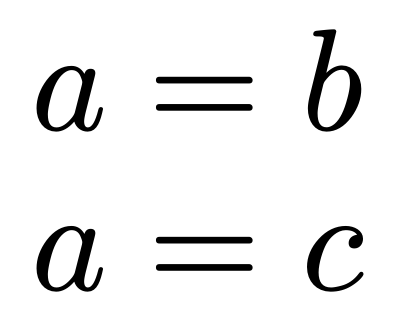

```mathematica
eqalign[{a==b,a==c}]//typmath[]
```

```mathematica
x^2//typmath[]
```

-Graphics-

```mathematica
Integrate[x,x]//typstep
```

-Graphics-

```mathematica
Integrate[x,x]//typstep
```

-Graphics-

```mathematica
Integrate[x,{x,0,y}]//typstep
```

-Graphics-

```mathematica
D[Exp[-x^2],{x,2},{y,2}]//typstep
```

-Graphics-

```mathematica
Exp@Max[x,y]+alpha[x,y]//typstep
```

-Graphics-

```mathematica
Series[Exp[x],{x,0,30}]//Normal//typstep
```

-Graphics-

```mathematica
D[f[x,y,z],x]//typstep
```

-Graphics-

```mathematica
1+1//typstep
```

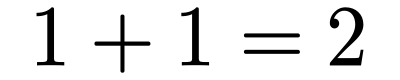

```mathematica
MatrixForm[{{1,2},{3,a}}]//typstep
```

-Graphics-

```mathematica
({{1},{2},{4+α}}//MatrixForm//typstep)
```

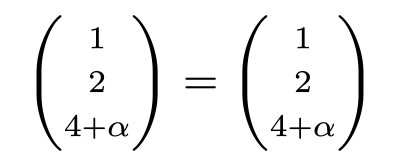

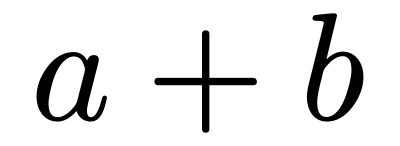

```mathematica
a+b//typmath[]
```

```mathematica
Conjugate[{I,x}]//typstep
```

-Graphics-

```mathematica
SuperStar[A1] (SuperStar[w1])^2 //typstep
```

-Graphics-

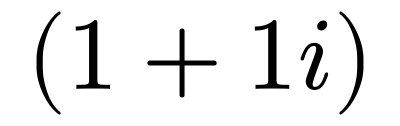

```mathematica
I+1//typmath[]
```